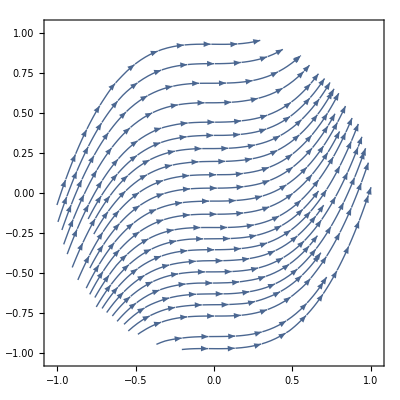

```mathematica
StreamPlot[
{1,3 x^2}
,{x,y}∈Disk[]]
```

```mathematica
FullSimplify[
Normalize[{1,f'[x]}].Normalize[{1,3 x^2}]==1,
{x,f[x],f'[x]}∈Reals]
```

√((1+9 x^4) (1+f'[x]^2))==1+3 x^2 f'[x]

```mathematica
DSolve[√((1+9 x^4) (1+f'[x]^2))==1+3 x^2 f'[x],{f[x]},{x}]
```

{{f[x]→x^3+C[1]}}

```mathematica
FullSimplify[
Normalize[{1,f'[x]}].Normalize[{1,g'[x]}]==1,
{x,f[x],f'[x],g'[x]}∈Reals]
```

√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x]

```mathematica
DSolve[√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x],{f[x],g[x]},{x}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x],{f[x],g[x]},{x}]

```mathematica
DSolve[√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x],{f[x]},{x}]
```

{{f[x]→C[1]+g[x]}}

```mathematica
FullSimplify[
Normalize[{h'[x],f'[x]}].Normalize[{j'[x],g'[x]}]==1,
{x,f'[x],g'[x],h'[x],j'[x]}∈Reals]
```

(f'[x] g'[x]+h'[x] j'[x])/(√((f'[x]^2+h'[x]^2) (g'[x]^2+j'[x]^2)))==1

```mathematica
DSolve[(f'[x] g'[x]+h'[x] j'[x])/(√((f'[x]^2+h'[x]^2) (g'[x]^2+j'[x]^2)))==1,{f[x],g[x],h[x],j[x]},{x}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[(f'[x] g'[x]+h'[x] j'[x])/(√((f'[x]^2+h'[x]^2) (g'[x]^2+j'[x]^2)))==1,{f[x],g[x],h[x],j[x]},{x}]

```mathematica
DSolve[(f'[x] g'[x]+h'[x] j'[x])/(√((f'[x]^2+h'[x]^2) (g'[x]^2+j'[x]^2)))==1,{f[x],h[x]},{x}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[(f'[x] g'[x]+h'[x] j'[x])/(√((f'[x]^2+h'[x]^2) (g'[x]^2+j'[x]^2)))==1,{f[x],h[x]},{x}]

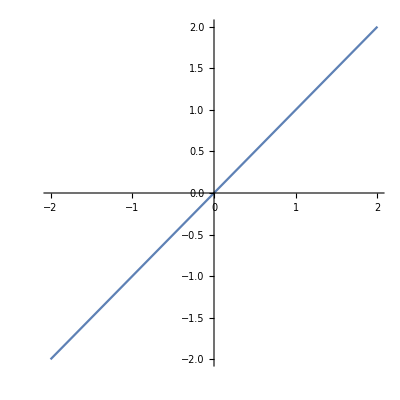

```mathematica
ParametricPlot[
{t,t}
,{t,-2,2}]
```

```mathematica
Manipulate[
ParametricPlot[
{t,t}.RotationMatrix[θ]
,{t,-2,2}]
,{θ,0,2π}]
```

```mathematica
Manipulate[
ParametricPlot[
{t,t}.(α RotationMatrix[θ])
,{t,-2,2}]
,{θ,0,2π},{α,0,1}]
```

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
ⅇ^(-x^2/2)
```

ⅇ^(-x^2/2)

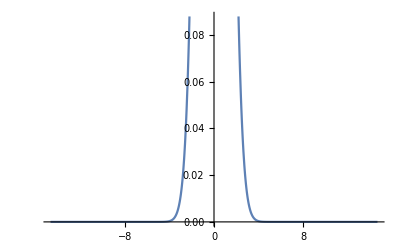

```mathematica
Plot[ⅇ^(-x^2/2),{x,-14.696938456699069,14.696938456699069}]
```

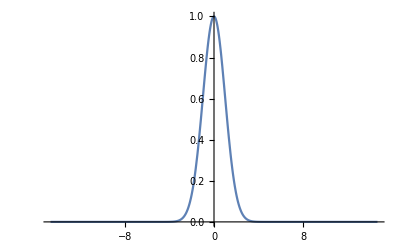

```mathematica
Plot[ⅇ^(-x^2/2),{x,-14.696938456699069,14.696938456699069},PlotRange->{0,1}]
```

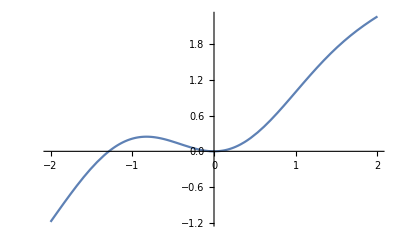

```mathematica
Plot[(1-ⅇ^(-x^2/2))x+(ⅇ^(-x^2/2))x^2,{x,-2,2}]
```

```mathematica
Normalize@{x,(1-ⅇ^(-x^2/2))x+(ⅇ^(-x^2/2))x^2}.
Normalize@{x,x^2}
```

x^2/(√(Abs[x]^2+Abs[x]^4) √(Abs[x]^2+Abs[(1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) x^2]^2))+(x^2 ((1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) x^2))/(√(Abs[x]^2+Abs[x]^4) √(Abs[x]^2+Abs[(1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) x^2]^2))

```mathematica
FullSimplify[
Normalize@{x,(1-ⅇ^(-x^2/2))x+(ⅇ^(-x^2/2))x^2}.
Normalize@{x,x^2},
x∈Reals]
```

(ⅇ^(-x^2/2) ((-1+x) x+ⅇ^(x^2/2) (1+x)))/(√((1+x^2) (1+ⅇ^(-x^2) (-1+ⅇ^(x^2/2)+x)^2)))

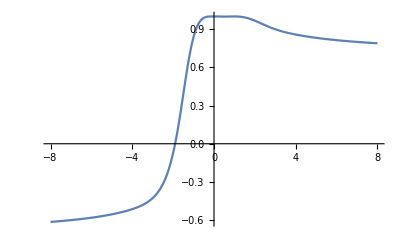

```mathematica
Plot[(ⅇ^(-x^2/2) ((-1+x) x+ⅇ^(x^2/2) (1+x)))/(√((1+x^2) (1+ⅇ^(-x^2) (-1+ⅇ^(x^2/2)+x)^2))),{x,-8,8}]
```



```mathematica
Plot[x x,{x,-2,2}]
```

```mathematica
∫_-1^0 f'[x]ⅆx
```

∫_-1^0 f'[x]ⅆx

```mathematica
n 10000
```

10000 n

```mathematica
10000+n 1
```

10000+n

```mathematica
10000 n/.n->1000
```

10000000

```mathematica
10000+n 1/.n->1000
```

11000

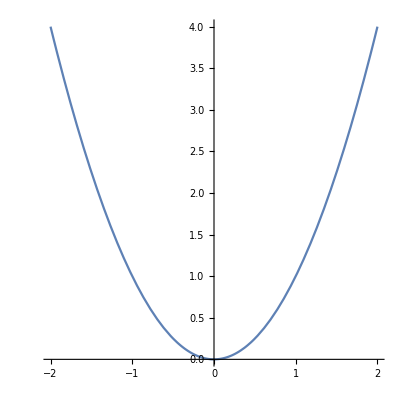

```mathematica
ParametricPlot[
{x,x^2}
,{x,-2,2}]
```

```mathematica
FullSimplify[
Normalize[D[{x,x^2},x]].
Normalize[D[{x,-x},x]]
,{x}∈Reals]
```

(1-2 x)/(√(2+8 x^2))

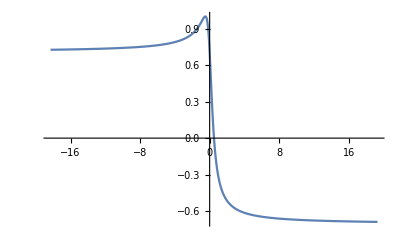

```mathematica
Plot[(1-2 x)/(√(2+8 x^2)),{x,-18.30666666666667,19.30666666666667}]
```

```mathematica
Laplacian[f[x],{x}]
```

f''[x]

```mathematica
Laplacian[x^2,{x}]
```

2

```mathematica
(f''[x] .f'[x])/f[x]
```

(f''[x].f'[x])/f[x]

```mathematica
With[{f=Function[x,x x]},
(f''[x].f'[x])/f[x]
]
```

(2.(2 x))/x^2

```mathematica
With[{f=Function[x,x x]},
(f''[x] . f'[x])/f[x]
]
```

(2.(2 x))/x^2

```mathematica
With[{f=Function[x,x x]},
(f''[x] x f'[x])/f[x]
]
```

4

```mathematica
With[{f=Function[x,x x]},
(f''[x] f'[x])/f[x]
]
```

4/x

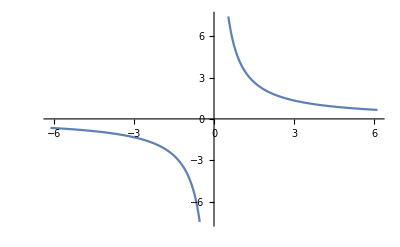

```mathematica
Plot[4/x,{x,-6.12,6.12}]
```

```mathematica
({x''[t],y''[t]}.{-y'[t],x'[t]})/Norm[{x'[t],y'[t]}]
```

```mathematica
({x''[t],y''[t]}.{-y'[t],x'[t]})/Norm[{x'[t],y'[t]}]
```

(-y'[t] x''[t]+x'[t] y''[t])/(√(Abs[x'[t]]^2+Abs[y'[t]]^2))

```mathematica
FullSimplify[
({x''[t],y''[t]}.{-y'[t],x'[t]})/Norm[{x'[t],y'[t]}]
,{t,x[t],y[t],x'[t],y'[t]}∈Reals]
```

(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^2+y'[t]^2))

```mathematica
FullSimplify[
({x''[t],y''[t]}.{-y'[t],x'[t]})/Norm[{x'[t],y'[t]}]^2
,{t,x[t],y[t],x'[t],y'[t]}∈Reals]
```

(-y'[t] x''[t]+x'[t] y''[t])/(x'[t]^2+y'[t]^2)

```mathematica
FullSimplify[
({x''[t],y''[t]}.{-y'[t],x'[t]})/Norm[{x'[t],y'[t]}]^3
,{t,x[t],y[t],x'[t],y'[t]}∈Reals]
```

(-y'[t] x''[t]+x'[t] y''[t])/((x'[t]^2+y'[t]^2)^(3/2))

```mathematica
With[{x=Identity},
FullSimplify[
({x''[t],y''[t]}.{-y'[t],x'[t]})/Norm[{x'[t],y'[t]}]^3
,{t,x[t],y[t],x'[t],y'[t]}∈Reals]
]
```

y''[t]/((1+y'[t]^2)^(3/2))

```mathematica
With[{x=Identity,y=Function[x, x x]},
FullSimplify[
({x''[t],y''[t]}.{-y'[t],x'[t]})/Norm[{x'[t],y'[t]}]^3
,{t,x[t],y[t],x'[t],y'[t]}∈Reals]
]
```

2/((1+4 t^2)^(3/2))

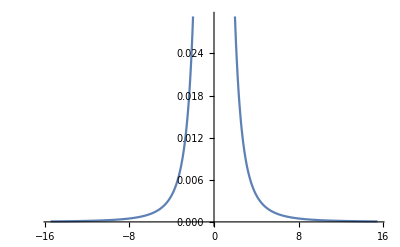

```mathematica
Plot[2/((1+4 t^2)^(3/2)),{t,-15.469999999999999,15.469999999999999}]
```

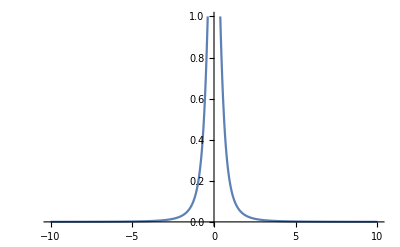

```mathematica
Plot[2/((1+4 t^2)^(3/2)),{t,-10,10},PlotRange->{0,1}]
```

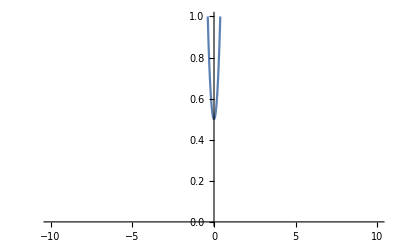

```mathematica
Plot[((1+4 t^2)^(3/2))/2,{t,-10,10},PlotRange->{0,1}]
```

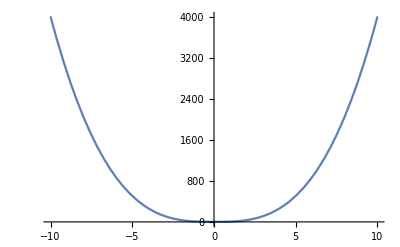

```mathematica
Plot[((1+4 t^2)^(3/2))/2,{t,-10,10}]
```

```mathematica
ParametricPlot[
{t Cos[t],t Sin[t]}
,{t,0,2π}]
```

```mathematica
Log[x]/x
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

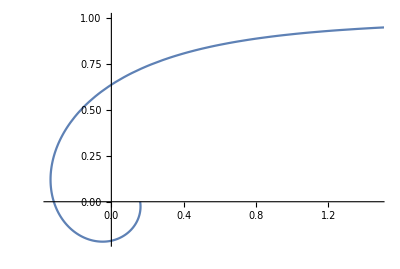

```mathematica
ParametricPlot[
{Cos[t]/t,Sin[t]/t}
,{t,0,2π}]
```

```mathematica
Log[x]/x
```

Log[x]/x

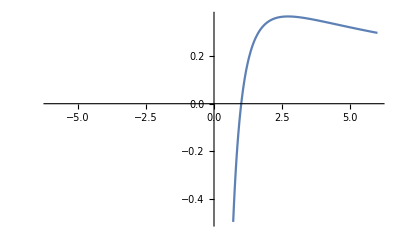

```mathematica
Plot[Log[x]/x,{x,-6,6}]
```

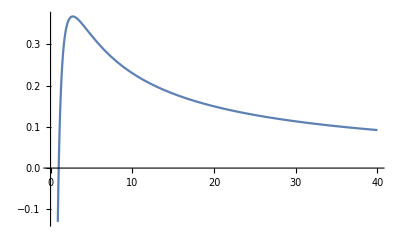

```mathematica
Plot[Log[x]/x,{x,0,40}]
```

```mathematica
Limit[Log[x]/x,x->∞]
```

0

```mathematica
Normalize[{x,x}].RotationMatrix[x]
```

{(x Cos[x])/(√2 Abs[x])+(x Sin[x])/(√2 Abs[x]),(x Cos[x])/(√2 Abs[x])-(x Sin[x])/(√2 Abs[x])}

```mathematica
FullSimplify[
Normalize[{x,x}].RotationMatrix[x]
,x∈Reals]
```

{(Sign[x] (Cos[x]+Sin[x]))/(√2),(Sign[x] (Cos[x]-Sin[x]))/(√2)}

```mathematica
FullSimplify[
Normalize[{x,x}].RotationMatrix[x]
,x∈Reals]
```

{(Sign[x] (Cos[x]+Sin[x]))/(√2),(Sign[x] (Cos[x]-Sin[x]))/(√2)}

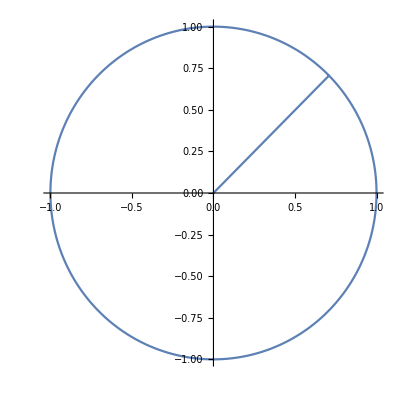

```mathematica
ParametricPlot[
{(Sign[x] (Cos[x]+Sin[x]))/(√2),(Sign[x] (Cos[x]-Sin[x]))/(√2)}
,{x,0,2π}]
```

```mathematica
Manipulate[
ParametricPlot[
{(Sign[x] (Cos[x]+Sin[x]))/(√2),(Sign[x] (Cos[x]-Sin[x]))/(√2)}
,{x,0,a}]
,{a,0,2π}]
```

ParametricPlot::plld: Endpoints for x in {x,0,FE`a$$194} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

```mathematica
FullSimplify[
Normalize[{x,x}].RotationMatrix[x θ]
,x∈Reals]
```

{(Sign[x] (Cos[x θ]+Sin[x θ]))/(√2),(Sign[x] (Cos[x θ]-Sin[x θ]))/(√2)}

```mathematica
FullSimplify[
Normalize[{x,x}].RotationMatrix[x θ]
,{x,θ}∈Reals]
```

{(Sign[x] (Cos[x θ]+Sin[x θ]))/(√2),(Sign[x] (Cos[x θ]-Sin[x θ]))/(√2)}